## Hand-in 2

Author: Aaron Beyen

### Question 1

```mathematica
b)
```

The energy function is given by:

```mathematica
En[s0_,s1_,s2_] := -s0+1/2*s1-1/2*s2+1/2*s0*s1+1/2*s1*s2
```

```mathematica
En[1,-1,1]
```

-3

By going through all combinations, one finds that E_min = -3

```mathematica
c)
```

We first define the relevant matrices for this question:

```mathematica
Z = {{1,0},{0,-1}};
```

```mathematica
Id= IdentityMatrix[2];
```

Now the Hamiltonian can be calculated using the tensor product:

```mathematica
Hc = KroneckerProduct[-Z,Id,Id]+1/2*KroneckerProduct[Id,Z,Id]-1/2*KroneckerProduct[Id,Id,Z]+1/2*KroneckerProduct[Z,Z,Id]+1/2*KroneckerProduct[Id,Z,Z];
```

```mathematica
MatrixForm[Hc]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2)

We are interested in the eigenvalues and eigenvectors:

```mathematica
Eigenvalues[Hc]
```

{-3,2,-1,1,1,0,0,0}

```mathematica
Eigenvectors[Hc]
```

{{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}}

So the lowest energy state corresponds to E = -3 with eigenstate {0,0,1,0,0,0,0,0}.

### Question 2

```mathematica
e)
```

#### Circuit calculations

We first define the relevant matrices for this question:

```mathematica
Z = {{1,0},{0,-1}};
```

```mathematica
X = {{0,1},{1,0}};
```

```mathematica
Id = IdentityMatrix[2];
```

```mathematica
H = 1/Sqrt[2] {{1,1},{1,-1}};
```

Then the Hamiltonians become:

```mathematica
Hc = KroneckerProduct[-Z,Id,Id]+1/2*KroneckerProduct[Id,Z,Id]-1/2*KroneckerProduct[Id,Id,Z]+1/2*KroneckerProduct[Z,Z,Id]+1/2*KroneckerProduct[Id,Z,Z];
```

```mathematica
Hm = KroneckerProduct[X,Id,Id] + KroneckerProduct[Id,X,Id] +KroneckerProduct[Id,Id,X] ;
```

We initially start in the |000>  state:

```mathematica
in = {1,0,0,0,0,0,0,0};
```

By applying the Hadamard gates and the matrix exponentials of the Hamiltonians, one finds the output state:

```mathematica
end = MatrixExp[-I*β*Hm].MatrixExp[-I*γ*Hc].KroneckerProduct[H,H,H].in;
```

```mathematica
end = FullSimplify[end,Assumptions->{β,γ}∈Reals]
```

{(ⅇ^(-ⅈ (3 β+2 γ)) (-(-1+ⅇ^(2 ⅈ β))^3-2 ⅇ^(ⅈ γ) (-1+ⅇ^(4 ⅈ β))+ⅇ^(2 ⅈ γ) (1+ⅇ^(2 ⅈ β)) (3+ⅇ^(4 ⅈ β))-8 ⅈ ⅇ^(3 ⅈ (β+γ)) Cos[β] (ⅇ^(2 ⅈ γ) Cos[β]-ⅈ Sin[β]) Sin[β]))/(16 √2),(ⅇ^(-ⅈ (3 β+2 γ)) ((-1+ⅇ^(2 ⅈ β))^2 (1+ⅇ^(2 ⅈ β))+ⅇ^(5 ⅈ γ) (-1+ⅇ^(2 ⅈ β))^2 (1+ⅇ^(2 ⅈ β))-2 ⅇ^(ⅈ γ) (-1+ⅇ^(4 ⅈ β))-8 ⅈ ⅇ^(3 ⅈ (β+γ)) Cos[β]^2 Sin[β]+ⅇ^(2 ⅈ γ) (3+ⅇ^(4 ⅈ β) (5-2 ⅈ Sin[2 β]))))/(16 √2),(ⅇ^(-ⅈ (3 β+2 γ)) (2 ⅇ^(ⅈ γ) (-1+ⅇ^(2 ⅈ β))^2+(-1+ⅇ^(2 ⅈ β))^2 (1+ⅇ^(2 ⅈ β))+ⅇ^(5 ⅈ γ) (1+ⅇ^(2 ⅈ β))^3-8 ⅈ ⅇ^(3 ⅈ (β+γ)) Cos[β]^2 Sin[β]+ⅇ^(2 ⅈ γ) (3+ⅇ^(4 ⅈ β) (-3-2 ⅈ Sin[2 β]))))/(16 √2),(ⅇ^(-ⅈ (3 β+2 γ)) (2 ⅇ^(ⅈ γ) (-1+ⅇ^(2 ⅈ β))^2+ⅇ^(3 ⅈ γ) (1+ⅇ^(2 ⅈ β))^3-8 ⅈ ⅇ^(3 ⅈ β) (1+ⅇ^(5 ⅈ γ)) Cos[β]^2 Sin[β]+ⅇ^(2 ⅈ γ) (3+ⅈ ⅇ^(4 ⅈ β) (3 ⅈ+2 Sin[2 β]))))/(16 √2),(ⅇ^(-ⅈ (3 β+2 γ)) (-ⅇ^(3 ⅈ γ) (-1+ⅇ^(2 ⅈ β))^3+(-1+ⅇ^(2 ⅈ β))^2 (1+ⅇ^(2 ⅈ β))+ⅇ^(5 ⅈ γ) (-1+ⅇ^(2 ⅈ β))^2 (1+ⅇ^(2 ⅈ β))+2 ⅇ^(ⅈ γ) (1+ⅇ^(2 ⅈ β))^2+ⅇ^(2 ⅈ γ) (3+ⅇ^(4 ⅈ β) (-3-2 ⅈ Sin[2 β]))))/(16 √2),(ⅇ^(-ⅈ (3 β+2 γ)) (-ⅇ^(5 ⅈ γ) (-1+ⅇ^(2 ⅈ β))^3+2 ⅇ^(ⅈ γ) (1+ⅇ^(2 ⅈ β))^2-8 ⅈ ⅇ^(3 ⅈ β) Cos[β]^2 Sin[β]-8 ⅇ^(3 ⅈ (β+γ)) Cos[β] Sin[β]^2+ⅇ^(2 ⅈ γ) (3+ⅇ^(4 ⅈ β) (-3+2 ⅈ Sin[2 β]))))/(16 √2),(ⅇ^(-ⅈ (3 β+2 γ)) (-8 ⅈ ⅇ^(3 ⅈ β) (1+ⅇ^(5 ⅈ γ)) Cos[β]^2 Sin[β]-8 ⅇ^(3 ⅈ (β+γ)) Cos[β] Sin[β]^2+ⅇ^(ⅈ γ) (2+3 ⅇ^(ⅈ γ)+ⅇ^(4 ⅈ β) (-2+ⅇ^(ⅈ γ) (5+2 ⅈ Sin[2 β])))))/(16 √2),(ⅇ^(-ⅈ (3 β+2 γ)) (ⅇ^(5 ⅈ γ) (-1+ⅇ^(2 ⅈ β))^2 (1+ⅇ^(2 ⅈ β))+(1+ⅇ^(2 ⅈ β))^3-2 ⅇ^(ⅈ γ) (-1+ⅇ^(4 ⅈ β))+ⅇ^(2 ⅈ γ) (3-3 ⅇ^(2 ⅈ β)+ⅇ^(4 ⅈ β)-ⅇ^(6 ⅈ β))-8 ⅈ ⅇ^(3 ⅈ (β+γ)) Cos[β]^2 Sin[β]))/(16 √2)}

#### Energy Calculation

Now that the final state is derived, we look for the expected value of the energy <γ,β|H_c |γ,β> :

```mathematica
Energy = FullSimplify[ComplexExpand[Conjugate[end]].Hc.end,Assumptions->{β,γ}∈Reals]
```

1/8 Sin[2 β] Sin[γ] (4 Cos[γ] (1+5 Cos[γ])+4 Cos[2 β] (1+Cos[γ]+2 Cos[2 γ])-2 Sin[2 β] (Sin[γ]+Sin[2 γ]+Sin[3 γ]))

```mathematica
Sin[2 β] Sin[γ] (4 Cos[γ] (1+5 Cos[γ])+4 Cos[2 β] (1+Cos[γ]+2 Cos[2 γ])-2 Sin[2 β] (Sin[γ]+Sin[2 γ]+Sin[3 γ]))
```

Sin[2 β] Sin[γ] (4 Cos[γ] (1+5 Cos[γ])+4 Cos[2 β] (1+Cos[γ]+2 Cos[2 γ])-2 Sin[2 β] (Sin[γ]+Sin[2 γ]+Sin[3 γ]))

Note that this energy E(β, γ) is periodic in β with period π and periodic in γ with period 2π, so it suffices to only look at β ∈ [0,π] and γ ∈ [0,2π]. We also note that 
E(β, γ) = E(π-β, 2π- γ) = symmetry of the energy function. This symmetry corresponds to flipping the energy around the line β = π/2 and the line γ = π simultaneously (see also figures below). As a consequence of this symmetry, if E(β*, γ*) is a global minimum, so is E(π-β*, 2π- γ*) --> global minima come in pairs (degeneracy).

```mathematica
Plot3D[Energy,{β,0, π },{γ,0,2 π},AxesOrigin->{0,0,0}, AxesLabel->{"β", "γ", "E"}, PlotLabel->"Energy landscape (β,γ)"]
```

-Graphics3D-

```mathematica
contour = ContourPlot[Energy, {β,0,π },{γ,0,2π}, PlotLegends->Automatic,FrameLabel->{"β", "γ"}];
```

```mathematica
p1 = ListPlot[{{2.50502, 0.681451},{0.63657,5.60173}}, PlotLegends->{"E_min angles"}, PlotStyle->Green , AxesLabel->{β,γ}, AxesOrigin->{0,0}];
```

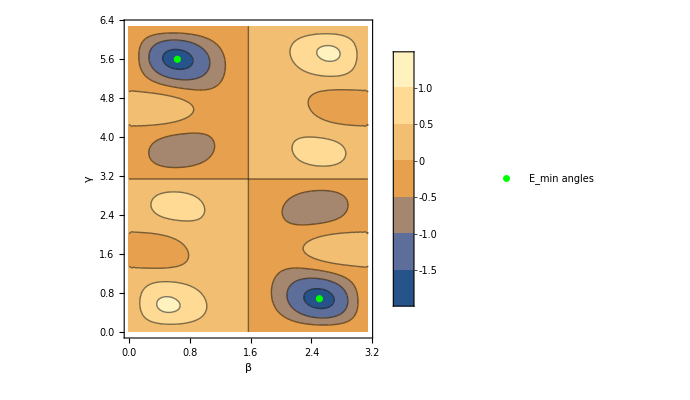

```mathematica
Show[contour,p1]
```

From these plots, it’s clear that there are 2 global minima for β ∈ [0,π] and γ ∈ [0,2π]. We can now calculate the angles that minimize the energy landscape:

```mathematica
anglem = NMinimize[{Energy,0<β<π,0<γ<2 π},{β,γ},Method->"RandomSearch"]
```

{-1.69496,{β→2.50502,γ→0.681451}}

The other global minimum (see discussion above) is then found at:

```mathematica
{π-2.5050230505843687, 2 π-0.6814512403078319}
```

{0.63657,5.60173}

So the minimal energy obtained for the p = 1 case equals E_min = -1.69496 for β*= 2.50502 and γ*= 0.681451 and for β*= 0.63657 and γ*= 5.60173.
In Question 1 b), we showed analytically that the groundstate has an energy E_min = -3. The difference with the QAOA result for p = 1 above arises because QAOA only gives an approximation to the groundstate. Decomposing the time evolution operator with only p = 1 timestep is an inefficient choice to get accurate results and higher values of p should lead to better approximations (see Question 3).

#### Success probability

```mathematica
f)
```

As shown in Question 1 c), the solution state is given by:

```mathematica
zsol = {0,0,1,0,0,0,0,0};
```

We can now calculate the algorithmic success probability as |<zsol|γ,β>|^2:

```mathematica
prob = FullSimplify[ComplexExpand[Abs[zsol.end]^2],Assumptions->{β,γ}∈Reals]
```

1/128 (18-2 Cos[4 β]-Cos[6 β]+Cos[2 β] (1-16 Cos[β]^3 Sin[β] (-2 Sin[2 γ]+Sin[3 γ]))-16 Cos[β]^3 Sin[β] ((-2 Cos[γ]+Cos[3 γ]+Cos[4 γ]+Cos[5 γ]) Sin[2 β]+4 Sin[2 γ]+3 Sin[3 γ]-2 Sin[β]^2 (-3 Sin[γ]+Sin[4 γ])))

Note that the success probability P (β, γ) satisfies P (β, γ) = P (π - β, 2 π - γ) = symmetry of the probability function . Therefore, to calculate the success probability for both global energy minima should lead to the same result, which is indeed the case:.

```mathematica
prob/.{β->anglem[[2,1,2]], γ->anglem[[2,2,2]]}
```

0.58846

```mathematica
probmin = prob/.{β->0.6365696030054244, γ->5.601734066871755}
```

0.58846

So the success probability for β*= 2.50502 and γ*= 0.681451 (and for β*= 0.63657 and γ*= 5.60173) equals 0.58846 = 58.846% (for p = 1) which is a bit higher than 50%. This outcome seems reasonable since E_min_QAOA/E_min_analytical = 0.564987 so that (roughly) the QAOA final state only gets the minimal energy correct up to a bit higher than 50%.

```mathematica
g)
```

As derived in the previous question, the success probability equals:

```mathematica
prob
```

1/128 (18-2 Cos[4 β]-Cos[6 β]+Cos[2 β] (1-16 Cos[β]^3 Sin[β] (-2 Sin[2 γ]+Sin[3 γ]))-16 Cos[β]^3 Sin[β] ((-2 Cos[γ]+Cos[3 γ]+Cos[4 γ]+Cos[5 γ]) Sin[2 β]+4 Sin[2 γ]+3 Sin[3 γ]-2 Sin[β]^2 (-3 Sin[γ]+Sin[4 γ])))

Note that the success probability P(β,γ) is periodic in β with period π and periodic in γ with period 2π, so it suffices to only look at β ∈ [0,π] and γ ∈ [0,2π]. We also note that P(β, γ) = P(π-β, 2π- γ) = symmetry of the probability function. As a consequence, if P(β’’, γ’’) is a global maximum, so is P(π-β’’, 2π- γ’’) --> global maxima come in pairs (degeneracy).

```mathematica
Plot3D[prob,{β,0, π},{γ,0,2π},PlotRange -> Full,AxesOrigin->{0,0,0}, AxesLabel->{"β", "γ", "P"}, PlotLabel->"Success probability(β,γ)"]
```

-Graphics3D-

```mathematica
contourp = ContourPlot[prob, {β,0,π },{γ,0,2π}, PlotLegends->Automatic,FrameLabel->{"β", "γ"}];
```

```mathematica
p2 = ListPlot[{{2.5244, 0.71258},{0.61719,5.57061}}, PlotLegends->{"P_max angles"} ,PlotStyle->Red ,AxesLabel->{β,γ}, AxesOrigin->{0,0}];
```

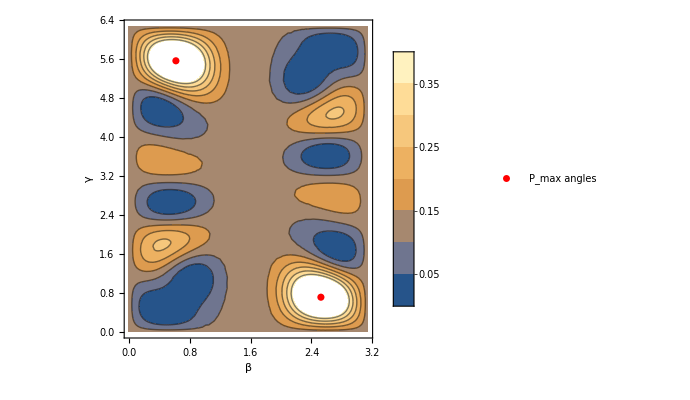

```mathematica
Show[contourp,p2]
```

```mathematica
pm = NMaximize[{prob,0<β<π,0<γ<2 π},{β,γ},Method->"RandomSearch"]
```

{0.591124,{β→2.5244,γ→0.71258}}

The other global minimum (see discussion above) is then found at :

```mathematica
{π-2.524403049773501, 2π-0.7125802708098158}
```

{0.61719,5.57061}

So the maximal probability obtained in the p = 1 case equals P_max = 0.591124 for β’’= 2.5244 and γ’’=0.71258 and for β’’= 0.61719 and γ’’= 5.57061. This maximal probability is a bit higher than 50%, which seems reasonable since E_min_QAOA/E_min_analytical = 0.564987 so that (roughly) the QAOA final state only gets the minimal energy correct up to a bit higher than 50%.

```mathematica
h)
```

The optimal angles for the energy are (β*= 2.50502, γ*= 0.681451) and (β*= 0.63657, γ*= 5.60173), while those for the probability equal (β’’= 2.5244,γ’’=0.71258) and (β’’= 0.61719, γ’’= 5.57061). When plotted, this gives:

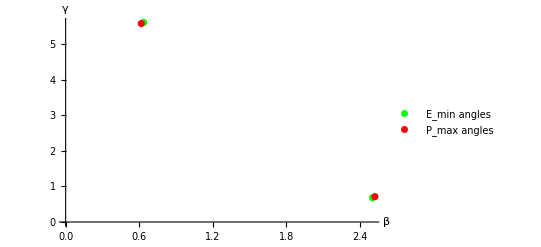

```mathematica
Show[p1,p2, AxesOrigin->{0,0}]
```

The differences for β are given by:

```mathematica
{Abs[2.524403049773501-2.5050230505843687],Abs[0.6171896038162923-0.6365696030054244]}
```

{0.01938,0.01938}

And the difference between the γ values:

```mathematica
{Abs[0.7125802708098158-0.681451240307832],Abs[5.601734066871755-5.570605036369771]}
```

{0.031129,0.031129}

As the above plots and calculation show, the angles obtained from minimising the energy or maximising the probability lie very close together, but are not equal to each other. Therefore, the ‘minimal energy state’ and ‘maximal probability state’ don’t truly coincide but are quite similar. It’s already a good sign that the QAOA algorithm, even for p = 1, is able to capture the fact that lower energy states are more probable. 
At first sight, the fact that the states aren’t identical seems paradoxical since normally,  the lowest energy state should have the maximal probability. In principle, this difference between the angles could be purely numerical, but I think there’s more to it. Indeed, one should remember that QAOA is only an approximation method to the true quantum evolution by dividing the time interval into discrete time steps. Therefore, it’s expected that typical properties of the states are only approximately correct. And since the difference is so small, it’s fair to say that QAOA did it’s job here.
Most likely, increasing the value of p will lead to a better approximation to the true ground state for which the maximum probability and minimal energy coincide. So increasing p should also make the difference between the angles of minimal energy and maximal probability go to zero asymptotically in p. It turns out that this is indeed the case: see question 3.

Overall conclusion for p = 1: Even for such a small value of p = 1, the QAOA algorithm is still able to capture quite good properties of the lowest energy state.

### Question 3

#### Circuit Calculation

We initially start in the |000>  state:

```mathematica
in = {1,0,0,0,0,0,0,0}
```

{1,0,0,0,0,0,0,0}

By applying the Hadamard gates (once) and the matrix exponentials of the Hamiltonians twice (p = 2), one finds the output state :

```mathematica
end3 =MatrixExp[-I*Subscript[β, 2]*Hm].MatrixExp[-I*Subscript[γ, 2]*Hc]. MatrixExp[-I*Subscript[β, 1]*Hm].MatrixExp[-I*Subscript[γ, 1]*Hc].KroneckerProduct[H,H,H].in;
```

```mathematica
end3 = Simplify[end3,Assumptions->{Subscript[β, 2] ,Subscript[β, 1] ,Subscript[γ, 2],Subscript[γ, 1]}∈Reals ];
```

#### Energy Calculation

Now that the final state is derived, we look for the expected value of the energy :

```mathematica
Energy3 =Re[Conjugate[end3].Hc.end3];
```

To get a feeling for how this energy function depends on the parameters β_1,β_2,γ_1 and γ_2, we plot some contourplots with 2 parameters at a time (and keep the other parameters fixed).

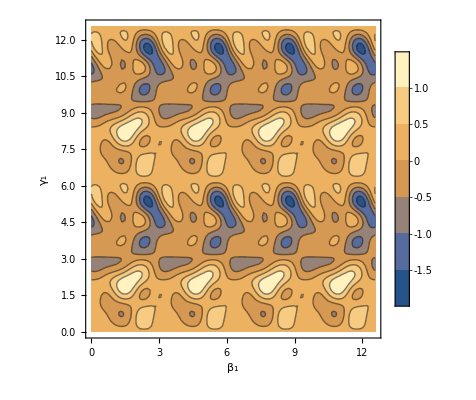

```mathematica
ContourPlot[Energy3/.{Subscript[β, 2] -> 1,Subscript[γ, 2] -> 1 }, {Subscript[β, 1],0,4π },{Subscript[γ, 1],0,4π}, PlotLegends->Automatic,FrameLabel->{Subscript[β, 1],Subscript[γ, 1]}]
```

From this plot, one can deduce that the energy is (most likely) periodic in β_1 with period π and periodic in γ_1 with period 2π. We say ‘most likely’ because a contourplot only gives a cross-section of the entire energy landscape, which makes it difficult to make general statements. As a consequence, it suffices to only look at β_1 ∈ [0,π] and γ_1 ∈ [0,2π] from now on.

```mathematica
ContourPlot[Energy3/.{Subscript[β, 1] -> 1,Subscript[γ, 1] -> 1 }, {Subscript[β, 2],0,4π },{Subscript[γ, 2],0,4π}, PlotLegends->Automatic,FrameLabel->{Subscript[β, 2],Subscript[γ, 2]}]
```

-Graphics-

From this plot one can deduce that the energy is (most likely) periodic in β_2 with period π and periodic in γ_2 with period 2π. As a consequence,it suffices to only look at β_2 ∈[0,π] and γ_2 ∈[0,2π].

We can now calculate the angles that minimise the energy landscape:

```mathematica
anglem3 = NMinimize[{Energy3,0<Subscript[β, 1]<π,0<Subscript[β, 2]<π, 0<Subscript[γ, 1]<2 π,0<Subscript[γ, 2]<2π },{Subscript[β, 1],Subscript[β, 2],Subscript[γ, 1],Subscript[γ, 2]},Method->"RandomSearch"]
```

{-2.72057,{β_1→2.32868,β_2→2.65112,γ_1→0.453204,γ_2→0.731779}}

So the minimal energy obtained in the p = 2 case equals E_min = -2.72057 for β_1*= 2.32868, β_2* = 2.65112 , γ_1*= 0.453204 and γ_2* = 0.731779. Most likely there will be some degeneracy in this case as well, but it’s difficult to determine exactly which angles will have the same global minimum. Note that this energy lies quite closer to the analytical result -3 than the p = 1 case. So increasing p, improves the result (as expected).

#### Probability Calculation

```mathematica
prob3 =Abs[zsol.end3]^2;
```

```mathematica
prob3min = prob3/.{Subscript[β, 1]->anglem3[[2,1,2]], Subscript[β, 2]->anglem3[[2,2,2]],Subscript[γ, 1]->anglem3[[2,3,2]],Subscript[γ, 2]->anglem3[[2,4,2]]}
```

0.891363

So the success probability for β_1*= 2.32868, β_2* = 2.65112 , γ_1*= 0.453204 and γ_2* = 0.731779 equals 0.891363 (for p = 2) . Note that this is quite larger than the result for p = 1. So increasing p, improves the result (as expected).

Conclusion for p = 2: As can clearly be seen, the results for p = 2 turn out to be much better than the p = 1 case . Indeed, the minimal energy lies closer to the expected analytical result and the success probability is larger . Therefore, one can conclude that if we take even larger values of p (f . e . p = 10) that the QAOA formalism will give an excellent approximation to the ground state .

### Continuation question 2 h)

Question 2h) asks to explain why the minimal energy angles and maximal probability angles don’t exactly agree. As explained above, I think this has to do with the fact that QAOA is only an approximation method, so that we only expect them to be approximately equal. As we concluded in the previous section, increasing p makes this approximation better so the angles should lie closer now:

First calculate the angles that maximize the success probability for p = 2:

```mathematica
NMaximize[{prob3,0<Subscript[β, 1]<π,0<Subscript[β, 2]<π, 0<Subscript[γ, 1]<2 π,0<Subscript[γ, 2]<2π },{Subscript[β, 1],Subscript[β, 2],Subscript[γ, 1],Subscript[γ, 2]},Method->"RandomSearch"]
```

{0.893409,{β_1→2.32613,β_2→2.6509,γ_1→0.46784,γ_2→0.759454}}

Thus, the maximum success probability for p = 2 equals 0.893409 for β_1’’ = 2.32613, β_2’’  = 2.6509 , γ_1’’ = 0.46784 and γ_2’’  = 0.759454 (again degeneracy is probable).

The differences for β_1:

```mathematica
Abs[2.326132654127922-2.3286765953134445]
```

0.00254394

The differences for β_2:

```mathematica
Abs[2.650904426021591-2.651122269327895]
```

0.000217843

The differences for γ_1:

```mathematica
Abs[0.4678400960526982-0.4532040391007482]
```

0.0146361

The differences for γ_2:

```mathematica
Abs[0.7594537818087901-0.7317785418193623]
```

0.0276752

Note that in each case, the angle difference is smaller than for the p = 1 case, especially for the β angles. Therefore, one can interpolate that increasing p will bring the minimal energy state and maximal probability state closer together and let them coincide asymptotically.